```mathematica
<<Combinatorica`
```

```mathematica
GV=Vertices[GridGraph[3,2]]
```

{{1.,1.},{2.,1.},{3.,1.},{1.,2.},{2.,2.},{3.,2.}}

```mathematica
{{1.,1.},{2.,1.},{3.,1.},{1.,2.},{2.,2.},{3.,2.}}
```

```mathematica
GE={{1,2},{2,3}}
```

{{1,2},{2,3}}

⁃Graph:<18,9,Directed>⁃

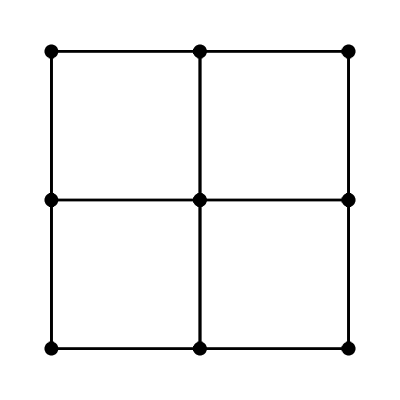

{1,4,5,6,9}

```mathematica
GG=Graph[{{{1,2},EdgeWeight->2},{{1,4}},{{2,3}},{{2,5}},{{3,6}},{{4,5}},{{4,7}},{{4,1}},{{5,6}},{{5,8}},{{5,2}},{{6,9}},{{6,3}},{{7,8}},{{7,4}},{{8,9}},{{8,5}},{{9,6}}},{{{0,0}},{{1,0}},{{2,0}},{{0,1}},{{1,1}},{{2,1}},{{0,2}},{{1,2}},{{2,2}}},EdgeDirection->True]

ShowGraph[GG]
ShortestPath[GG,1,9]
```

⁃Graph:<7,6,Undirected>⁃

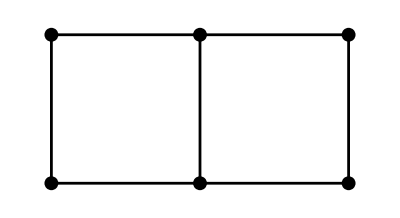

{{1.,1.},{2.,1.},{3.,1.},{1.,2.},{2.,2.},{3.,2.}}

{{1,2},{2,3},{4,5},{5,6},{1,4},{2,5},{3,6}}

```mathematica
G=GridGraph[3,2]
ShowGraph[G]
Vertices[G]
Edges[G]
```

```mathematica
Needs["GraphUtilities`"]
```

GraphCoordinates::shdw: Symbol GraphCoordinates appears in multiple contexts GraphUtilities`Global`; definitions in context GraphUtilities` may shadow or be shadowed by other definitions.